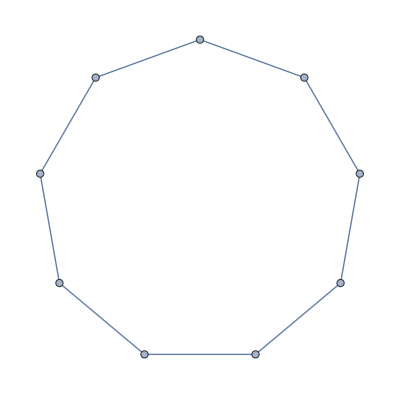

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

1

```mathematica
r=50;
n=50;

figure=CirclePoints[r,n];
drawTheFig={Line[AppendTo[figure,figure[[1]]]],PointSize[Large],Point[figure]};
Point[figure];
Graphics[drawTheFig];

exGraph={1<->2,2<->3,3<->1};
CycleGraph[9]
IncidenceMatrix[CycleGraph[9]] //MatrixForm
MeanGraphDistance[exGraph]
```